```mathematica
SetDirectory[SystemDialogInput["Directory"]]
```

D:\saveAndLoad

```mathematica
SetDirectory["D:\\newLight3\\"]
```

D:\newLight3

```mathematica
GetParent[orgNo_]:=Module[{path,g,n,s,i},
Quiet[
path = StringForm["organisms\\org``.json",orgNo];
{g,n,s,i}=Import[path//ToString];
"parent"/.i
]
]
GetLivingOrganisms[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["output\\frame``.csv",frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
organisms="o"/.items//DeleteDuplicates;
Select[organisms,#>=0&]
]
```

```mathematica
GetGeneration[org_]:=Length[NestWhileList[GetParent,org,#≥0&]]-1
```

```mathematica
Import["organisms\\org0.json"]
```

{genome→{vertices→{{i→0,type→0,f→2},{i→1,type→0,f→2},{i→2,type→0,f→2},{i→3,type→0,f→2},{i→4,type→2,f→2},{i→5,type→2,f→2},{i→6,type→2,f→2},{i→7,type→2,f→2},{i→8,type→2,f→2},{i→9,type→2,f→2},{i→10,type→2,f→2},{i→11,type→2,f→2},{i→12,type→2,f→2},{i→13,type→2,f→2},{i→14,type→2,f→2},{i→15,type→3,f→2}},links→{{i→15,o→4,w→0.5},{i→1,o→10,w→-2.},{i→15,o→13,w→0.5}},radius→{1,1,1}},nervesystem→{vertices→{{i→0,type→2,f→2},{i→1,type→2,f→2},{i→2,type→2,f→2}},links→{}},step→0,parent→-1}

```mathematica
NestWhileList[GetParent,2,#≥0&]
```

{2,0,-1}

```mathematica
step = 1160000;
currGenomeIndex = 635552;
```

```mathematica
edges =ParallelMap[GetParent[#]->#&,Table[o,{o,0,currGenomeIndex}]];
```

```mathematica
living = GetLivingOrganisms[step];
```

```mathematica
g=Graph[edges];
```

```mathematica
Graph[edges,GraphHighlight->(living∩VertexList[g]),VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
living
```

{255782,255783,255784,255786,255787,255790,255791,255792,255794,255796,255800,255801,255802,255803,255804,255805,255806,255807,255808,255809,255810,255811,255812,255813,255815,255818,255819,255820,255821,255822,255823,255827,255828,255829,255831,255832,255833,255834,255835,255837,255841,255843,255844,255845,255846,255847,255848,255849,255850,255851,255852,255853,255854,255855,255857,255858,255859,255860,255861,255862,255866,255867,255868,255869,255870,255871,255873,255874,255878,255879,255880,255883,255884,255886,255887,255888,255889,255890,255891,255893,255894,255895,255896,255897,255898,255899,255900,255901,255902,255903,255905,255906,255907,255908,255909,255910,255911,255912,255913,255914,255915,255916,255917,255918,255919,255920,255921,255922,255923,255924,255925,255926,255927,255928,255929,255930,255931,255932,255933,255935,255936,255937,255938,255940,255941,255943,255945,255946,255947,255948,255949,255951,255952,255953,255954,255955,255956,255957,255958,255959,255960,255961,255962,255963,255964,255965,255966,255968,255969,255970,255971,255972,255973,255974,255975,255976,255977,255978,255979,255980,255981,255983,255984,255985,255986,255987,255988,255989,255990,255991,255992,255993,255994,255995,255996,255997,255998,255999,256000,256001,256002,256003,256004,256005}

```mathematica
GetGeneration[255782]
```

603

```mathematica
generations=Map[GetGeneration,living]
```

{603,614,609,603,611,603,606,609,613,601,611,613,612,609,612,617,613,612,607,607,601,611,603,607,615,618,607,607,606,608,602,601,612,604,602,610,613,613,616,608,613,601,608,613,603,615,614,602,608,615,601,607,608,611,604,610,611,611,608,610,604,616,615,612,616,610,613,603,608,603,603,613,608,614,601,602,616,609,604,613,603,607,602,604,608,601,603,604,615,611,619,603,612,612,608,607,608,610,607,602,607,618,614,614,615,607,614,612,605,613,602,612,613,601,612,607,610,604,612,608,603,611,607,601,611,602,607,608,612,602,611,605,615,605,614,608,614,616,610,603,605,604,610,609,617,613,613,608,613,604,602,608,608,602,608,613,601,612,616,613,616,612,607,616,608,611,604,604,611,616,613,614,604,608,602,615,612,612,604,609,619,613,603,614}

```mathematica
Max[generations]
```

619

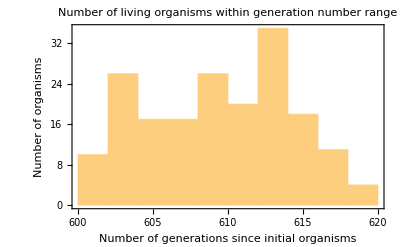

```mathematica
Histogram[
generations,
FrameLabel->{
"Number of generations since initial organisms",
"Number of organisms"},
PlotLabel->"Number of living organisms within generation number range",
Frame->{{True,False},{True,False}}]
```

```mathematica
parents=ParallelMap[GetParent,Table[o,{o,0,currGenomeIndex}]];
```

```mathematica
nParents=Transpose[Tally[parents]][[2]]; 
nInfertile=currGenomeIndex-CountDistinct[parents]-1; (* -1 because parent with id "-1" should not be counted *)
nOneChild=Count[nParents,1];
nTwoChildren=Count[nParents,2];
nMoreThanTwo=Count[nParents,u_/;u> 2];
val={nInfertile,nOneChild,nTwoChildren,nMoreThanTwo};
```

```mathematica
On[Assert];
Assert[Total[val]+1==currGenomeIndex];
Off[Assert];
```

```mathematica
pie=PieChart[val,ChartLegends->Placed[{
StringForm["No children (`` orgs)",val⟦1⟧],
StringForm["One child (`` orgs)",val⟦2⟧],
StringForm["Two children (`` orgs)",val⟦3⟧],
StringForm[">2 children (`` orgs)",val⟦4⟧]
},Right],
ChartLabels->Placed[StringForm["``%",N[(100#)/Total[val],3]]&/@val,"RadialOutside"],
ChartLabels->"%",ImageSize->250]
```

-Graphics-

```mathematica
nParentsWithHierless=Join[nParents,Table[0,nInfertile]];
```

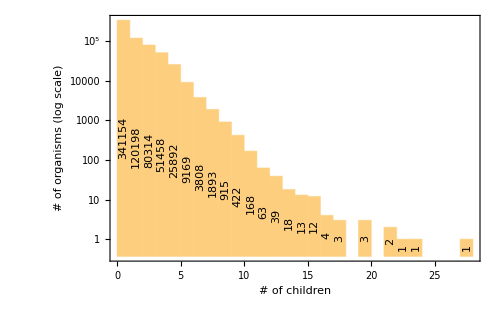

```mathematica
plot=Histogram[
nParentsWithHierless,
LabelingFunction->(Placed[Rotate[#1,π/2],Center]&),
ImageSize->500,
Frame->{{True,False},{True,False}},
FrameLabel->{"# of children","# of organisms (log scale)"},
ScalingFunctions->"Log",
PlotRange->All
]
```

```mathematica
Max[nParents]
```

27

```mathematica
Mean[nParents]//N
```

2.15883

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\nChildrenHistogram.eps",plot]
```

C:\Users\admin\Documents\Joakim\repo\grafiliv\doc\figs\nChildrenHistogram.eps

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\nChildrenPie.eps",pie]
```

C:\Users\admin\Documents\Joakim\repo\grafiliv\doc\figs\nChildrenPie.eps

```mathematica
Median[nParents]//N
```

2.